# Exam 3

## Problem 2

```mathematica
n=1;
Subscript[k, b]=1.3807*10^-23;
B=1;
Subscript[u, b]=9.2740*10^-24;
alpha=(5*Subscript[u, b]*B)/(Subscript[k, b]*T)
n*Subscript[k, b]*alpha^2*(Sech[alpha])^2
```

3.35844/T

(1.55731×10^-22 Sech[3.35844/T]^2)/T^2

General::munfl: Sech[3287.98] is too small to represent as a normalized machine number; precision may be lost.

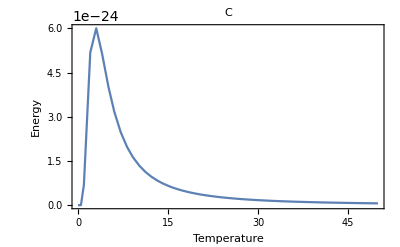

```mathematica
Plot[n*Subscript[k, b]*(((5*Subscript[u, b]*B)/(Subscript[k, b]*T))^2*(Sech[(5*Subscript[u, b]*B)/(Subscript[k, b]*T)])^2),{T,0,50},{Frame->True,PlotRange->All,BaseStyle->{FontSize->12},PlotLabel->C,FrameLabel->{"Temperature","Energy"}}]
```

```mathematica
f[T_]:=n*Subscript[k, b]*((5*Subscript[u, b]*B)/(Subscript[k, b]*T))^2*(Sech[(5*Subscript[u, b]*B)/(Subscript[k, b]*T)])^2
valueofc=MaxValue[n*Subscript[k, b]*((5*Subscript[u, b]*B)/(Subscript[k, b]*T))^2*(Sech[(5*Subscript[u, b]*B)/(Subscript[k, b]*T)])^2,T]
f[2.8]
tempofpeak=2.8
```

6.06443×10^-24

6.06443×10^-24

2.8

```mathematica
valueofc
tempofpeak
```

6.06443×10^-24

2.8

## Problem 4

```mathematica
(6*Exp[-0/(0.08618*300)]+6*Exp[-25/(0.08618*300)])^-1*6*Exp[-25/(0.08618*300)]
```

0.275485

```mathematica
((4*Exp[-0/(0.08618*300)]+Exp[-25/(0.08618*300)])^-1*Exp[-25/(0.08618*300)])*25
```

2.17017

```mathematica
((Exp[-0/(0.08618*300)]+Exp[-25/(0.08618*300)])^-1*Exp[-25/(0.08618*300)])*25
```

6.88713

```mathematica
6.88713/300+(0.08618)*Log[Exp[-0/(0.08618*300)]+Exp[-25/(0.08618*300)]]
```

0.0507289

## Problem 5

```mathematica
((17+4-1)!)/(17!*(4-1)!)
```

1140

```mathematica
0.1*Log[1140]
```

0.703878

```mathematica
((17+2-1)!)/(17!*(2-1)!)
```

18

```mathematica
N[18/1140]
```

0.0157895

```mathematica
N[2^17/4^17]
```

7.62939×10^-6

```mathematica
1/(0.1*Log[(19/2+1)/(19/2-1)])
```

47.324

## Problem 6

```mathematica
Subscript[n, Q]=(((3.35*10^-27)*Subscript[k, b]*300)/(2*Pi*(1.055*10^-34)^2))^(3/2)
Subscript[n, conc]=101325/(Subscript[k, b]*300)
```

2.79493×10^30

2.44622×10^25

```mathematica
Subscript[n, Q]/Subscript[n, conc]
```

114255.

```mathematica
Subscript[v, peak]=Sqrt[2*0.08618*300/(3.35*10^-27)]
```

1.24239×10^14

```mathematica
K=1/2*3.35*10^-27*Subscript[v, peak]^2
```

25.854

```mathematica
K/(1.609*10^-22)
```

25.7433

```mathematica
i=(3.35*10^-27)*(74*10^-12)^2+(3.35*10^-27)*(74*10^-12)^2
```

3.66892×10^-47

```mathematica
thetarot=((1.055*10^-34)^2)/(2*i*Subscript[k, b])
```

10.9859

```mathematica
300/thetarot
```

27.3076

```mathematica
Subscript[C, v]=3*Subscript[k, b]*6.023*10^23
```

24.9479

```mathematica
0.5*Csch[0.5/300*(0.5*((74*10^-12)*1.25*10^14)^2(3.35*10^-27))/(1.38*10^-23)]
```

3.03995×10^-8